# HW 6: 4.2 CE # 3, 7 4.3 # 2, 3, 5, 6, 7, 8

## Cole Pendergraft

```mathematica
dividedDifference[t_]:=
Module[{m,xData,yData,n},(*We'll locally hold a matrix, the x,y data, and the length of t*)
n=Length[t]; (*Indexing is always confusing, this "should be" n+1, but bear with me*)
m=Table[0,{n},{n}]; (*This is where the table will live*)
xData=Transpose[t][[1]];yData=Transpose[t][[2]]; (*grab the x's and y's*)
m[[1]]=yData; m=Transpose[m]; (*The first column of dd's is the y-values*)
For[col=2,col≤n,col++,(*First iterate through columns*)
For[entry=col,entry≤n,entry++,(*In a column, start at the diagonal and iterate DOWN*)
m[[entry]][[col]]=(m[[entry]][[col-1]]-m[[entry-1]][[col-1]])/(xData[[entry]]-xData[[entry-col+1]])
(*The indexing is tricky, and would be easier if the first column was the "0" column*)]
];
Return[m]]
```

```mathematica
newtonForm[t_]:=
Module[{coeffs,xData, sum,prod,n},(*We'll need to grab the xData again for the roots, and then keep a table of coefficients*)
n=Length[t];xData=Transpose[t][[1]];
coeffs=Diagonal[dividedDifference[t]];sum=coeffs[[1]];(*Initialize with the constant term*)
prod=1;
For[term=1,term<n,term++,(*Remember, we're building a degree n-1 poly*)
prod*=(x-xData[[term]]);
sum+=coeffs[[term+1]]*prod (*1st coefficient is already there, so we're going from 2 to n*)
];
Return[sum];
]
```

## 4.2 CE # 3

Using procedures corresponding to the pseudocode in the text, find a polynomial of degree 13 that interpolates f(x) = arctan(x) on the interval [-1, 1]. Test numerically by taking 100 points to determine how accurate the polynomial approximation is.

I believe I have found the pseudocode in the textbook that this problem is referencing, but I’m not sure I’m familiar enough with the Mathematica language and syntax to properly convert that pseudocode into a working code. I approached this problem in the way I knew how to; I created a data table, then an interpolating polynomial, and then another data table in matrix form that demostrates the error associated with each calculation.

Create a data table of 15 values between x = [-1, 1]. For some reason when I try to use 13 values I only get a polynomial of degree 11, so I’ve had to use a couple extra points in order to get a degree 13 polynomial.

```mathematica
Clear[data, f, p, Er];
f[x_] = ArcTan[x];
data = Table[{.14285714285i, f[.14285714285i]}, {i, -7, 7}]
```

{{-1.,-0.785398},{-0.857143,-0.708626},{-0.714286,-0.620249},{-0.571429,-0.519146},{-0.428571,-0.404892},{-0.285714,-0.2783},{-0.142857,-0.141897},{0.,0.},{0.142857,0.141897},{0.285714,0.2783},{0.428571,0.404892},{0.571429,0.519146},{0.714286,0.620249},{0.857143,0.708626},{1.,0.785398}}

```mathematica
p[x_] = Simplify[newtonForm[data]]
```

6.14743×10^-17+1. x+1.38778×10^-17 x^2-0.333307 x^3-5.55112×10^-17 x^4+0.199474 x^5+6.93889×10^-18 x^6-0.138408 x^7+2.77556×10^-17 x^8+0.0921256 x^9+6.93889×10^-18 x^10-0.0456183 x^11+3.46945×10^-18 x^12+0.011133 x^13

```mathematica
Er[x_] = Abs[p[x] - f[x]];
MatrixForm[Table[{"i =", 0.02i , "f[i]=",f[0.02i],"p[i]=" , p[0.02i],"Error =", Er[0.02i]}, {i, -50, 50}]]
```

(i = | -1. | f[i]= | -0.785398 | p[i]= | -0.785398 | Error = | 3.25295×10^-14
i = | -0.98 | f[i]= | -0.775297 | p[i]= | -0.775289 | Error = | 8.21906×10^-6
i = | -0.96 | f[i]= | -0.764993 | p[i]= | -0.764983 | Error = | 0.0000100399
i = | -0.94 | f[i]= | -0.75448 | p[i]= | -0.754471 | Error = | 8.7273×10^-6
i = | -0.92 | f[i]= | -0.743756 | p[i]= | -0.743749 | Error = | 6.2509×10^-6
i = | -0.9 | f[i]= | -0.732815 | p[i]= | -0.732811 | Error = | 3.70492×10^-6
i = | -0.88 | f[i]= | -0.721655 | p[i]= | -0.721653 | Error = | 1.61478×10^-6
i = | -0.86 | f[i]= | -0.710271 | p[i]= | -0.710271 | Error = | 1.5644×10^-7
i = | -0.84 | f[i]= | -0.69866 | p[i]= | -0.698661 | Error = | 6.91464×10^-7
i = | -0.82 | f[i]= | -0.686818 | p[i]= | -0.686819 | Error = | 1.04594×10^-6
i = | -0.8 | f[i]= | -0.674741 | p[i]= | -0.674742 | Error = | 1.05523×10^-6
i = | -0.78 | f[i]= | -0.662426 | p[i]= | -0.662427 | Error = | 8.61049×10^-7
i = | -0.76 | f[i]= | -0.64987 | p[i]= | -0.649871 | Error = | 5.79426×10^-7
i = | -0.74 | f[i]= | -0.63707 | p[i]= | -0.637071 | Error = | 2.93747×10^-7
i = | -0.72 | f[i]= | -0.624023 | p[i]= | -0.624023 | Error = | 5.54237×10^-8
i = | -0.7 | f[i]= | -0.610726 | p[i]= | -0.610726 | Error = | 1.11252×10^-7
i = | -0.68 | f[i]= | -0.597177 | p[i]= | -0.597176 | Error = | 2.02427×10^-7
i = | -0.66 | f[i]= | -0.583373 | p[i]= | -0.583373 | Error = | 2.27752×10^-7
i = | -0.64 | f[i]= | -0.569313 | p[i]= | -0.569313 | Error = | 2.04163×10^-7
i = | -0.62 | f[i]= | -0.554996 | p[i]= | -0.554996 | Error = | 1.50885×10^-7
i = | -0.6 | f[i]= | -0.54042 | p[i]= | -0.540419 | Error = | 8.58306×10^-8
i = | -0.58 | f[i]= | -0.525584 | p[i]= | -0.525584 | Error = | 2.33752×10^-8
i = | -0.56 | f[i]= | -0.510488 | p[i]= | -0.510488 | Error = | 2.66908×10^-8
i = | -0.54 | f[i]= | -0.495133 | p[i]= | -0.495133 | Error = | 5.9263×10^-8
i = | -0.52 | f[i]= | -0.479519 | p[i]= | -0.479519 | Error = | 7.33603×10^-8
i = | -0.5 | f[i]= | -0.463648 | p[i]= | -0.463648 | Error = | 7.11616×10^-8
i = | -0.48 | f[i]= | -0.44752 | p[i]= | -0.44752 | Error = | 5.68717×10^-8
i = | -0.46 | f[i]= | -0.431139 | p[i]= | -0.431139 | Error = | 3.56049×10^-8
i = | -0.44 | f[i]= | -0.414507 | p[i]= | -0.414507 | Error = | 1.24192×10^-8
i = | -0.42 | f[i]= | -0.397628 | p[i]= | -0.397628 | Error = | 8.41504×10^-9
i = | -0.4 | f[i]= | -0.380506 | p[i]= | -0.380506 | Error = | 2.38743×10^-8
i = | -0.38 | f[i]= | -0.363147 | p[i]= | -0.363147 | Error = | 3.2373×10^-8
i = | -0.36 | f[i]= | -0.345556 | p[i]= | -0.345556 | Error = | 3.37187×10^-8
i = | -0.34 | f[i]= | -0.327739 | p[i]= | -0.327738 | Error = | 2.88835×10^-8
i = | -0.32 | f[i]= | -0.309703 | p[i]= | -0.309703 | Error = | 1.96569×10^-8
i = | -0.3 | f[i]= | -0.291457 | p[i]= | -0.291457 | Error = | 8.24505×10^-9
i = | -0.28 | f[i]= | -0.273009 | p[i]= | -0.273009 | Error = | 3.1232×10^-9
i = | -0.26 | f[i]= | -0.254368 | p[i]= | -0.254368 | Error = | 1.25334×10^-8
i = | -0.24 | f[i]= | -0.235545 | p[i]= | -0.235545 | Error = | 1.86305×10^-8
i = | -0.22 | f[i]= | -0.21655 | p[i]= | -0.21655 | Error = | 2.07527×10^-8
i = | -0.2 | f[i]= | -0.197396 | p[i]= | -0.197396 | Error = | 1.89506×10^-8
i = | -0.18 | f[i]= | -0.178093 | p[i]= | -0.178093 | Error = | 1.3903×10^-8
i = | -0.16 | f[i]= | -0.158655 | p[i]= | -0.158655 | Error = | 6.75204×10^-9
i = | -0.14 | f[i]= | -0.139096 | p[i]= | -0.139096 | Error = | 1.11279×10^-9
i = | -0.12 | f[i]= | -0.119429 | p[i]= | -0.119429 | Error = | 8.288×10^-9
i = | -0.1 | f[i]= | -0.0996687 | p[i]= | -0.0996686 | Error = | 1.35736×10^-8
i = | -0.08 | f[i]= | -0.07983 | p[i]= | -0.07983 | Error = | 1.61467×10^-8
i = | -0.06 | f[i]= | -0.0599282 | p[i]= | -0.0599281 | Error = | 1.56703×10^-8
i = | -0.04 | f[i]= | -0.0399787 | p[i]= | -0.0399787 | Error = | 1.23252×10^-8
i = | -0.02 | f[i]= | -0.0199973 | p[i]= | -0.0199973 | Error = | 6.76461×10^-9
i = | 0. | f[i]= | 0. | p[i]= | 6.14743×10^-17 | Error = | 6.14743×10^-17
i = | 0.02 | f[i]= | 0.0199973 | p[i]= | 0.0199973 | Error = | 6.76461×10^-9
i = | 0.04 | f[i]= | 0.0399787 | p[i]= | 0.0399787 | Error = | 1.23252×10^-8
i = | 0.06 | f[i]= | 0.0599282 | p[i]= | 0.0599281 | Error = | 1.56703×10^-8
i = | 0.08 | f[i]= | 0.07983 | p[i]= | 0.07983 | Error = | 1.61467×10^-8
i = | 0.1 | f[i]= | 0.0996687 | p[i]= | 0.0996686 | Error = | 1.35736×10^-8
i = | 0.12 | f[i]= | 0.119429 | p[i]= | 0.119429 | Error = | 8.288×10^-9
i = | 0.14 | f[i]= | 0.139096 | p[i]= | 0.139096 | Error = | 1.11279×10^-9
i = | 0.16 | f[i]= | 0.158655 | p[i]= | 0.158655 | Error = | 6.75204×10^-9
i = | 0.18 | f[i]= | 0.178093 | p[i]= | 0.178093 | Error = | 1.3903×10^-8
i = | 0.2 | f[i]= | 0.197396 | p[i]= | 0.197396 | Error = | 1.89506×10^-8
i = | 0.22 | f[i]= | 0.21655 | p[i]= | 0.21655 | Error = | 2.07527×10^-8
i = | 0.24 | f[i]= | 0.235545 | p[i]= | 0.235545 | Error = | 1.86305×10^-8
i = | 0.26 | f[i]= | 0.254368 | p[i]= | 0.254368 | Error = | 1.25334×10^-8
i = | 0.28 | f[i]= | 0.273009 | p[i]= | 0.273009 | Error = | 3.1232×10^-9
i = | 0.3 | f[i]= | 0.291457 | p[i]= | 0.291457 | Error = | 8.24505×10^-9
i = | 0.32 | f[i]= | 0.309703 | p[i]= | 0.309703 | Error = | 1.96569×10^-8
i = | 0.34 | f[i]= | 0.327739 | p[i]= | 0.327738 | Error = | 2.88835×10^-8
i = | 0.36 | f[i]= | 0.345556 | p[i]= | 0.345556 | Error = | 3.37187×10^-8
i = | 0.38 | f[i]= | 0.363147 | p[i]= | 0.363147 | Error = | 3.2373×10^-8
i = | 0.4 | f[i]= | 0.380506 | p[i]= | 0.380506 | Error = | 2.38743×10^-8
i = | 0.42 | f[i]= | 0.397628 | p[i]= | 0.397628 | Error = | 8.41504×10^-9
i = | 0.44 | f[i]= | 0.414507 | p[i]= | 0.414507 | Error = | 1.24192×10^-8
i = | 0.46 | f[i]= | 0.431139 | p[i]= | 0.431139 | Error = | 3.56049×10^-8
i = | 0.48 | f[i]= | 0.44752 | p[i]= | 0.44752 | Error = | 5.68717×10^-8
i = | 0.5 | f[i]= | 0.463648 | p[i]= | 0.463648 | Error = | 7.11616×10^-8
i = | 0.52 | f[i]= | 0.479519 | p[i]= | 0.479519 | Error = | 7.33603×10^-8
i = | 0.54 | f[i]= | 0.495133 | p[i]= | 0.495133 | Error = | 5.9263×10^-8
i = | 0.56 | f[i]= | 0.510488 | p[i]= | 0.510488 | Error = | 2.66908×10^-8
i = | 0.58 | f[i]= | 0.525584 | p[i]= | 0.525584 | Error = | 2.33752×10^-8
i = | 0.6 | f[i]= | 0.54042 | p[i]= | 0.540419 | Error = | 8.58306×10^-8
i = | 0.62 | f[i]= | 0.554996 | p[i]= | 0.554996 | Error = | 1.50885×10^-7
i = | 0.64 | f[i]= | 0.569313 | p[i]= | 0.569313 | Error = | 2.04163×10^-7
i = | 0.66 | f[i]= | 0.583373 | p[i]= | 0.583373 | Error = | 2.27752×10^-7
i = | 0.68 | f[i]= | 0.597177 | p[i]= | 0.597176 | Error = | 2.02427×10^-7
i = | 0.7 | f[i]= | 0.610726 | p[i]= | 0.610726 | Error = | 1.11252×10^-7
i = | 0.72 | f[i]= | 0.624023 | p[i]= | 0.624023 | Error = | 5.54237×10^-8
i = | 0.74 | f[i]= | 0.63707 | p[i]= | 0.637071 | Error = | 2.93747×10^-7
i = | 0.76 | f[i]= | 0.64987 | p[i]= | 0.649871 | Error = | 5.79426×10^-7
i = | 0.78 | f[i]= | 0.662426 | p[i]= | 0.662427 | Error = | 8.61049×10^-7
i = | 0.8 | f[i]= | 0.674741 | p[i]= | 0.674742 | Error = | 1.05523×10^-6
i = | 0.82 | f[i]= | 0.686818 | p[i]= | 0.686819 | Error = | 1.04594×10^-6
i = | 0.84 | f[i]= | 0.69866 | p[i]= | 0.698661 | Error = | 6.91464×10^-7
i = | 0.86 | f[i]= | 0.710271 | p[i]= | 0.710271 | Error = | 1.5644×10^-7
i = | 0.88 | f[i]= | 0.721655 | p[i]= | 0.721653 | Error = | 1.61478×10^-6
i = | 0.9 | f[i]= | 0.732815 | p[i]= | 0.732811 | Error = | 3.70492×10^-6
i = | 0.92 | f[i]= | 0.743756 | p[i]= | 0.743749 | Error = | 6.2509×10^-6
i = | 0.94 | f[i]= | 0.75448 | p[i]= | 0.754471 | Error = | 8.7273×10^-6
i = | 0.96 | f[i]= | 0.764993 | p[i]= | 0.764983 | Error = | 0.0000100399
i = | 0.98 | f[i]= | 0.775297 | p[i]= | 0.775289 | Error = | 8.21906×10^-6
i = | 1. | f[i]= | 0.785398 | p[i]= | 0.785398 | Error = | 3.27516×10^-14)

## 4.2 CE # 7

Let f(x) = max[0, 1 - x]. Sketch the function f. Then find interpolating polynomials of degrees 2, 4, 8, 16, and 32 to f on the interval [-4, 4], using equally spaced nodes. Print out the discrepancy f(x) - p(x) at 128 equally spaced points. Then redo the problem using Chebyshev nodes.

I’m getting some really weird behavior with my code in this problem. For some reason I can’t generate interpolating polynomials with the data I’m producing, instead I get a list of values. I think my approach is correct, but my lack of fluency in mathematica is causing me to make some error in my code that is ultimately causing my attempts to fail. This was the last question on this assignment I attempted and unfortuantely there are no more office hours available. I included my thought process below, hopefully I was approaching the problem correctly even though my code ultimately didn’t do what I needed it to do.

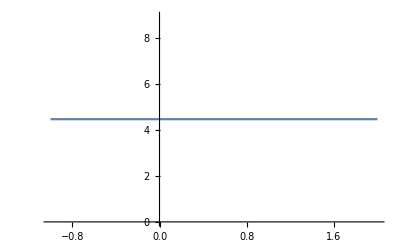

```mathematica
Clear[f, g];
f[x_] = Max[0, 1-x];
g = Plot[f[x], {x, -1, 2}]
```

```mathematica
Ds[x_] = f[x] - p[x]; (* Simple function for calculating discrepancy *)
```

```mathematica
Clear[data, p];
(* Degree 2 polynomial *)
data = Table[{4i, f[4i]}, {i, -1, 1}]; (* [-1, 1] is within the interval [-4, 4] *)
p[x_]=Simplify[newtonForm[data]]
```

{{1+2 √3},{1+2 √3},{1+2 √3}}

```mathematica
MatrixForm[Table[{"i =", 0.0625i, "f[i] =", f[0.0625i], "p[i] =", p[0.0625i], "Discrepancy =", Ds[0.0625i]}, {i, -64, 64}]]
```

(i = | -4. | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.9375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.8125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.75 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.6875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.5625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.5 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.4375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.3125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.25 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.1875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.0625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3. | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.9375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.8125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.75 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.6875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.5625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.5 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.4375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.3125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.25 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.1875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.0625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2. | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.9375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.8125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.75 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.6875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.5625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.5 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.4375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.3125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.25 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.1875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.0625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1. | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.9375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.8125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.75 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.6875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.5625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.5 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.4375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.3125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.25 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.1875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.0625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0. | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.0625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.1875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.25 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.3125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.4375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.5 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.5625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.6875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.75 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.8125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.9375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1. | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.0625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.1875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.25 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.3125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.4375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.5 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.5625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.6875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.75 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.8125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.9375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2. | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.0625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.1875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.25 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.3125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.4375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.5 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.5625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.6875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.75 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.8125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.9375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3. | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.0625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.1875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.25 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.3125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.4375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.5 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.5625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.6875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.75 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.8125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.9375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 4. | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}})

```mathematica
Clear[data, p];
(* Degree 4 polynomial *)
data = Table[{2i, f[2i]}, {i, -2, 2}]; (* [-2, 2] is within the interval [-4, 4] *)
p[x_]=Simplify[newtonForm[data]]
```

{{1+2 √3},{1+2 √3},{1+2 √3}}

```mathematica
MatrixForm[Table[{"i =", 0.0625i, "f[i] =", f[0.0625i], "p[i] =", p[0.0625i], "Discrepancy =", Ds[0.0625i]}, {i, -64, 64}]]
```

(i = | -4. | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.9375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.8125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.75 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.6875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.5625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.5 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.4375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.3125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.25 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.1875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.0625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3. | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.9375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.8125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.75 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.6875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.5625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.5 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.4375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.3125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.25 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.1875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.0625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2. | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.9375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.8125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.75 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.6875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.5625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.5 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.4375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.3125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.25 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.1875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.0625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1. | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.9375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.8125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.75 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.6875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.5625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.5 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.4375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.3125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.25 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.1875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.0625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0. | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.0625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.1875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.25 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.3125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.4375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.5 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.5625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.6875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.75 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.8125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.9375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1. | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.0625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.1875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.25 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.3125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.4375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.5 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.5625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.6875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.75 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.8125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.9375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2. | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.0625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.1875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.25 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.3125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.4375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.5 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.5625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.6875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.75 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.8125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.9375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3. | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.0625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.1875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.25 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.3125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.4375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.5 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.5625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.6875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.75 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.8125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.9375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 4. | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}})

```mathematica
Clear[data, p];
(* Degree 8 polynomial *)
data = Table[{i, f[i]}, {i, -4, 4}];
p[x_]=Simplify[newtonForm[data]]
```

{{1+2 √3},{1+2 √3},{1+2 √3}}

```mathematica
MatrixForm[Table[{"i =", 0.0625i, "f[i] =", f[0.0625i], "p[i] =", p[0.0625i], "Discrepancy =", Ds[0.0625i]}, {i, -64, 64}]]
```

(i = | -4. | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.9375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.8125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.75 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.6875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.5625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.5 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.4375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.3125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.25 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.1875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3.0625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -3. | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.9375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.8125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.75 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.6875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.5625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.5 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.4375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.3125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.25 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.1875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2.0625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -2. | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.9375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.8125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.75 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.6875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.5625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.5 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.4375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.3125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.25 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.1875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1.0625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -1. | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.9375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.8125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.75 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.6875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.5625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.5 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.4375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.3125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.25 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.1875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | -0.0625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0. | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.0625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.1875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.25 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.3125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.4375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.5 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.5625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.6875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.75 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.8125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 0.9375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1. | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.0625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.1875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.25 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.3125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.4375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.5 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.5625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.6875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.75 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.8125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 1.9375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2. | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.0625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.1875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.25 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.3125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.4375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.5 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.5625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.6875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.75 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.8125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 2.9375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3. | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.0625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.1875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.25 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.3125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.4375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.5 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.5625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.625 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.6875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.75 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.8125 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.875 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 3.9375 | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}}
i = | 4. | f[i] = | 1+2 √3 | p[i] = | {{1+2 √3},{1+2 √3},{1+2 √3}} | Discrepancy = | {{0},{0},{0}})

```mathematica
Clear[data, p];
(* Degree 16 polynomial *)
data = Table[{0.5i, f[0.5i]}, {i, -8, 8}];
p[x_]=Simplify[newtonForm[data]]
```

{{4.4641},{4.4641},{4.4641}}

```mathematica
MatrixForm[Table[{"i =", 0.0625i, "f[i] =", f[0.0625i], "p[i] =", p[0.0625i], "Discrepancy =", Ds[0.0625i]}, {i, -64, 64}]]
```

(i = | -4. | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -3.9375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -3.875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -3.8125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -3.75 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -3.6875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -3.625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -3.5625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -3.5 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -3.4375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -3.375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -3.3125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -3.25 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -3.1875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -3.125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -3.0625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -3. | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -2.9375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -2.875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -2.8125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -2.75 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -2.6875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -2.625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -2.5625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -2.5 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -2.4375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -2.375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -2.3125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -2.25 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -2.1875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -2.125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -2.0625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -2. | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -1.9375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -1.875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -1.8125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -1.75 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -1.6875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -1.625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -1.5625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -1.5 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -1.4375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -1.375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -1.3125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -1.25 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -1.1875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -1.125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -1.0625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -1. | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -0.9375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -0.875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -0.8125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -0.75 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -0.6875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -0.625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -0.5625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -0.5 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -0.4375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -0.375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -0.3125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -0.25 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -0.1875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -0.125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -0.0625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 0. | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 0.0625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 0.125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 0.1875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 0.25 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 0.3125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 0.375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 0.4375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 0.5 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 0.5625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 0.625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 0.6875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 0.75 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 0.8125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 0.875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 0.9375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 1. | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 1.0625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 1.125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 1.1875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 1.25 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 1.3125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 1.375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 1.4375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 1.5 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 1.5625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 1.625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 1.6875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 1.75 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 1.8125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 1.875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 1.9375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 2. | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 2.0625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 2.125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 2.1875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 2.25 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 2.3125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 2.375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 2.4375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 2.5 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 2.5625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 2.625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 2.6875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 2.75 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 2.8125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 2.875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 2.9375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 3. | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 3.0625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 3.125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 3.1875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 3.25 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 3.3125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 3.375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 3.4375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 3.5 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 3.5625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 3.625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 3.6875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 3.75 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 3.8125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 3.875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 3.9375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 4. | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}})

```mathematica
Clear[data, p];
(* Degree 32 polynomial *)
data = Table[{0.25i, f[0.25i]}, {i, -16, 16}];
p[x_]=Simplify[newtonForm[data]]
```

{{4.4641},{4.4641},{4.4641}}

```mathematica
MatrixForm[Table[{"i =", 0.0625i, "f[i] =", f[0.0625i], "p[i] =", p[0.0625i], "Discrepancy =", Ds[0.0625i]}, {i, -64, 64}]]
```

(i = | -4. | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -3.9375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -3.875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -3.8125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -3.75 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -3.6875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -3.625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -3.5625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -3.5 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -3.4375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -3.375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -3.3125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -3.25 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -3.1875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -3.125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -3.0625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -3. | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -2.9375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -2.875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -2.8125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -2.75 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -2.6875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -2.625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -2.5625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -2.5 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -2.4375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -2.375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -2.3125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -2.25 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -2.1875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -2.125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -2.0625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -2. | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -1.9375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -1.875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -1.8125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -1.75 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -1.6875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -1.625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -1.5625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -1.5 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -1.4375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -1.375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -1.3125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -1.25 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -1.1875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -1.125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -1.0625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -1. | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -0.9375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -0.875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -0.8125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -0.75 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -0.6875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -0.625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -0.5625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -0.5 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -0.4375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -0.375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -0.3125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -0.25 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -0.1875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -0.125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | -0.0625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 0. | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 0.0625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 0.125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 0.1875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 0.25 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 0.3125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 0.375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 0.4375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 0.5 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 0.5625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 0.625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 0.6875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 0.75 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 0.8125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 0.875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 0.9375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 1. | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 1.0625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 1.125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 1.1875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 1.25 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 1.3125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 1.375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 1.4375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 1.5 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 1.5625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 1.625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 1.6875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 1.75 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 1.8125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 1.875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 1.9375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 2. | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 2.0625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 2.125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 2.1875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 2.25 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 2.3125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 2.375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 2.4375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 2.5 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 2.5625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 2.625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 2.6875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 2.75 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 2.8125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 2.875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 2.9375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 3. | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 3.0625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 3.125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 3.1875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 3.25 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 3.3125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 3.375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 3.4375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 3.5 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 3.5625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 3.625 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 3.6875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 3.75 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 3.8125 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 3.875 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 3.9375 | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}}
i = | 4. | f[i] = | 1+2 √3 | p[i] = | {{4.4641},{4.4641},{4.4641}} | Discrepancy = | {{0.},{0.},{0.}})

Now we are going to go through the same problem using Chebyshev nodes.

Our textbook defines the set of Chebyshev nodes on the interval [a, b] follows:

x_i = 1/2(a + b) + 1/2(b - a)cos[((2i + 1)/(2n + 2))π]

```mathematica
Clear[nodes, data, p];
(* CNG = Chebyshev Node Generator, use n=2 for second degree polynomial *)
CNG[i_] = -4Cos[((2i + 1 )/6)Pi];
nodes = Table[{CNG[4i]}, {i, -1, 1}]
```

{{2 √3},{-2 √3},{0}}

```mathematica
data = Table[{CNG[4i], f[CNG[4i]]}, {i, -1., 1.}]
```

{{3.4641,1+2 √3},{-3.4641,1+2 √3},{7.34788×10^-16,1+2 √3}}

```mathematica
p[x_]=Simplify[newtonForm[data]]
```

{{4.4641},{4.4641},{4.4641}}

```mathematica
Clear[nodes, data, p];
(* Use n=4 for fourth degree polynomial *)
CNG[i_] = -4Cos[((2i + 1 )/10)Pi];
nodes = Table[{CNG[2i]}, {i, -2, 2}]
```

{{4 √(5/8-(√5)/8)},{-4 √(5/8-(√5)/8)},{-4 √(5/8+(√5)/8)},{0},{4 √(5/8+(√5)/8)}}

```mathematica
data = Table[{CNG[2i], f[CNG[2i]]}, {i, -2., 2.}]
```

{{2.35114,1+2 √3},{-2.35114,1+2 √3},{-3.80423,1+2 √3},{-2.44929×10^-16,1+2 √3},{3.80423,1+2 √3}}

```mathematica
p[x_] = Simplify[newtonForm[data]]
```

{{4.4641},{4.4641},{4.4641}}

```mathematica
Clear[nodes, data, p];
(* Use n=8 for eighth degree polynomial *)
CNG[i_] = -4Cos[((2i + 1 )/18)Pi];
nodes = Table[{CNG[i]}, {i, -4, 4}]
```

{{-4 Sin[π/9]},{-4 Sin[(2 π)/9]},{-2 √3},{-4 Cos[π/18]},{-4 Cos[π/18]},{-2 √3},{-4 Sin[(2 π)/9]},{-4 Sin[π/9]},{0}}

```mathematica
data = Table[{CNG[i], f[CNG[i]]}, {i, -4., 4.}]
```

{{-1.36808,1+2 √3},{-2.57115,1+2 √3},{-3.4641,1+2 √3},{-3.93923,1+2 √3},{-3.93923,1+2 √3},{-3.4641,1+2 √3},{-2.57115,1+2 √3},{-1.36808,1+2 √3},{-2.44929×10^-16,1+2 √3}}

```mathematica
p[x_] = Simplify[newtonForm[data]]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{{Indeterminate},{Indeterminate},{Indeterminate}}

```mathematica
Clear[nodes, data, p];
(* Use n=16 for sixteenth degree polynomial *)
CNG[i_] = -4Cos[((2i + 1 )/34)Pi];
nodes = Table[{CNG[0.5i]}, {i, -8, 8}]
```

{{-3.19207},{-3.40087},{-3.58065},{-3.72989},{-3.8473},{-3.93189},{-3.98294},{-4.},{-3.98294},{-3.93189},{-3.8473},{-3.72989},{-3.58065},{-3.40087},{-3.19207},{-2.95604},{-2.69478}}

```mathematica
data = Table[{CNG[0.5i], f[CNG[0.5i]]}, {i, -8., 8.}]
```

{{-3.19207,1+2 √3},{-3.40087,1+2 √3},{-3.58065,1+2 √3},{-3.72989,1+2 √3},{-3.8473,1+2 √3},{-3.93189,1+2 √3},{-3.98294,1+2 √3},{-4.,1+2 √3},{-3.98294,1+2 √3},{-3.93189,1+2 √3},{-3.8473,1+2 √3},{-3.72989,1+2 √3},{-3.58065,1+2 √3},{-3.40087,1+2 √3},{-3.19207,1+2 √3},{-2.95604,1+2 √3},{-2.69478,1+2 √3}}

```mathematica
p[x_] = newtonForm[data]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{{Indeterminate},{Indeterminate},{Indeterminate}}

```mathematica
Clear[nodes, data, p];
(* Use n=32 for sixteenth degree polynomial *)
CNG[i_] = -4Cos[((2i + 1 )/66)Pi];
nodes = Table[{CNG[0.25i]}, {i, -16, 16}]
```

{{-3.78},{-3.81007},{-3.83797},{-3.8637},{-3.88725},{-3.90859},{-3.92771},{-3.94462},{-3.95929},{-3.97171},{-3.98189},{-3.98981},{-3.99547},{-3.99887},{-4.},{-3.99887},{-3.99547},{-3.98981},{-3.98189},{-3.97171},{-3.95929},{-3.94462},{-3.92771},{-3.90859},{-3.88725},{-3.8637},{-3.83797},{-3.81007},{-3.78},{-3.7478},{-3.71347},{-3.67704},{-3.63853}}

```mathematica
data = Table[{CNG[0.25i], f[CNG[0.5i]]}, {i, -16., 16.}]
```

{{-3.78,1+2 √3},{-3.81007,1+2 √3},{-3.83797,1+2 √3},{-3.8637,1+2 √3},{-3.88725,1+2 √3},{-3.90859,1+2 √3},{-3.92771,1+2 √3},{-3.94462,1+2 √3},{-3.95929,1+2 √3},{-3.97171,1+2 √3},{-3.98189,1+2 √3},{-3.98981,1+2 √3},{-3.99547,1+2 √3},{-3.99887,1+2 √3},{-4.,1+2 √3},{-3.99887,1+2 √3},{-3.99547,1+2 √3},{-3.98981,1+2 √3},{-3.98189,1+2 √3},{-3.97171,1+2 √3},{-3.95929,1+2 √3},{-3.94462,1+2 √3},{-3.92771,1+2 √3},{-3.90859,1+2 √3},{-3.88725,1+2 √3},{-3.8637,1+2 √3},{-3.83797,1+2 √3},{-3.81007,1+2 √3},{-3.78,1+2 √3},{-3.7478,1+2 √3},{-3.71347,1+2 √3},{-3.67704,1+2 √3},{-3.63853,1+2 √3}}

```mathematica
p[x_] = newtonForm[data]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{{Indeterminate},{Indeterminate},{Indeterminate}}

## 4.3 # 2

Using Taylor series, establish the error term for the formula

						f’(0) ≈ 1/(2h)[f(2h) - f(0)]

I can tell from the f(2h) that this is a function of the form f(x + 2h), which would be:

f(x + 2h) = f(x) + 2hf’(x) + 2h^2 f''(ξ)

If we solve for f’(x), we get:

f’(x) = 1/(2h)[f(x + 2h) - f(x)] - hf’’(ξ)

and if we sub in x = 0:

f’(0) = 1/(2h)[f(2h) - f(0)] - hf’’(ξ)

with an error term of -hf’’(ξ).

## 4.3 # 3

Derive the approximation formula
				f’(x) ≈ 1/(2h)[4f(x + h) - 3f(x) - f(x + 2h)]
and show that its error term is of the form 1/3 h^2 f ’’’(ξ ).

Start with

f(x + 2h) = f(x) + 2hf’(x) + 2 h^2f’’(x) + (8 h^3)/6f'''(ξ_1)

4f(x + h) = 4f(x) + 4hf’(x) + 2h^2f’’(x) + (4 h^3)/6f'''(ξ_2)

Now solve for f(x + h) - f(x + 2h)

4f(x + h) - f(x + 2h) = 4f(x) + 4hf’(x) + 2h^2f’’(x) + (4 h^3)/6f'''(ξ_2) - (f(x) + 2hf’(x) + 2 h^2f’’(x) + (8 h^3)/6f'''(ξ_1))
⟹ 4f(x) + 4hf’(x) + 2h^2f’’(x) + (4 h^3)/6f'''(ξ_2) - f(x) - 2hf’(x) - 2 h^2f’’(x) - (8 h^3)/6f'''(ξ_1)
⟹ 4f(x + h) - f(x + 2h) = 3f(x) + 2hf’(x) - h^3/3(4f’’’(ξ_1) - 2f’’’(ξ_2))

Now we just need to solve for f’(x)

⟹ 4f(x + h) - f(x + 2h) - 3f(x) = 2hf’(x) - h^3/3(4f’’’(ξ_1) - 2f’’’(ξ_2))
⟹2hf’(x) = 4f(x + h) - f(x + 2h) - 3f(x) + h^3/3(4f’’’(ξ_1) - 2f’’’(ξ_2))
⟹ f’(x) = 1/(2h)[4f(x + h) - f(x + 2h) - 3f(x)] + h^2/6(4f’’’(ξ_1) - 2f’’’(ξ_2))
⟹ f’(x) = 1/(2h)[4f(x + h) - f(x + 2h) - 3f(x)] + h^2/3(2f’’’(ξ_1) - f’’’(ξ_2))

So now we have derived f’(x) = 1/(2h)[4f(x + h) - f(x + 2h) - 3f(x)], and we can also see that our error term is h^2/3(2f’’’(ξ_1) - f’’’(ξ_2)), which I believe is of the form 1/3 h^2 f ‘’’(ξ ). The 2 attached to f’’’(ξ_1) throws me a bit, but I believe that even with that the error term still matches exactly what we are looking for.

## 4.3 # 5

Averaging the forward-difference formula f’(x) ≈ [f(x + h) - f(x)]/h and the backward-difference formula f’(x) ≈ [f(x) - f(x - h)]/h, each with error term O(h), results in the central-difference formula f’(x) ≈ [f(x + h) - f(x-h)]/(2h) with error O(h^2). Show why. Hint: Determine at least the first term in the error series for each formula.

We start with 

f(x + h) = f(x) + hf’(x) + h^2/2f’’(x) + h^3/6f’’’( ξ_1)

f(x - h) = f(x) - hf’(x) + h^2/2f’’(x) - h^3/6f’’’( ξ_2)

and compute f(x + h) - f(x -h)

f(x + h) - f(x - h) = 2hf’(x) + 1/6h^2 ((f'''(ξ_1) + f'''(ξ_2))/2)

What we notice now is that part of our error term is ((f'''(ξ_1) + f'''(ξ_2))/2) which is actually the average of two values of f’’’. By the Mean Value Theorem, this means that there exists some ξ_3 in between (ξ_1, ξ_2) where f’’’(ξ_3) = ((f'''(ξ_1) + f'''(ξ_2))/2). This means we can actually simplify our error term to be 1/6h^2 (f'''(ξ_3)), which is a good reason to go our to f’’’ rather than f’’. Furthermore, this means that 1/6h^2 (f'''(ξ_3)) = O(h^2) , because we have f’’(x) = 0, which is why our error term is O(h^2).

## 4.3 # 6

Criticize the following analysis. By Taylor’s formula, we have

		f(x + h) - f(x) = hf’(x) + h^2/2f’’(x) + h^3/6f’’’(ξ)
		
		f(x - h) - f(x) = -hf’(x) + h^2/2f’’(x) - h^3/6f’’’(ξ)
		
So by adding, we obtain an exact expression for f’’(x):

		f(x + h) + f(x - h) - 2f(x) = h^2f’’(x)
		
Criticisms:
	The major issue I see with this is that error term should not be cancelled in the way it is shown here. Here we have two entirely different functions, f(x+h) - f(x) and f(x-h) - f(x), which means both function has its own error value. I.e. h^3/6f’’’(ξ_1)  is not necessarily equal to h^3/6f’’’(ξ_2). These error terms should still be attached to the final equation:
		
	f(x + h) + f(x - h) - 2f(x) = h^2f’’(x) + h^3/6(f’’’(ξ_1) - f’’’(ξ_2))
	
With this in mind, using the term “exact” to describe this equation is inaccurate, our error terms are still a piece of the function and therefore prevent this from being exact.

## 4.3 # 7

Criticize the following analysis. By Taylor’s formula, we have

                    f(x + h) - f(x) = hf’(x) + h^2/2f’’(x) + h^3/6f’’’(ξ)
		
		f(x - h) - f(x) = -hf’(x) + h^2/2f’’(x) - h^3/6f’’’(ξ)
		
Therefore,
                    1/h^2[f(x + h) - 2f(x) + f(x - h)] = f’’(x) + h/6[f’’’(ξ_1) - f’’’(ξ_2)]
                    
 The error in the approximation formula for f’’ is thus O(h).
 
 Criticisms:
 	There is no general function called O(h). O(h) is the terminology we use to describe the error as a function of h, and that error function will vary greatly depending on the initial functions. So to say that “The error approximation formula for f’’ is thus O(h)” is far too vague to accurately describe what is happening. Rather, the writer should have said “The error in the approximation formula for f’’ is thus O(h) = h/6[f’’’(ξ_1) - f’’’(ξ_2)]”.

## 4.3 # 8

Derive the two formulas

	a. f’(x) ≈ 1/(4h)[f(x + 2h) - f(x - 2h)]
	
	b. f’’(x) ≈ 1/(4 h^2)[f(x + 2h) - 2f(x) + f(x - 2h)]

and establish formulas for the errors in using them.

a:
	Start with
	
	f(x + 2h) = f(x) + 2hf’(x) + 2h^2 f''(ξ_1)
	
	f(x - 2h) = f(x) - 2hf’(x) + 2 h^2 f''(ξ_2)
	
	then solve for f(x + 2h) - f(x - 2h):
	
	f(x + 2h) - f(x - 2h) = f(x) + 2hf’(x) + 2 h^2 f''(ξ_1) - (f(x) - 2hf’(x) + 2 h^2 f''(ξ_2))
	
	⟹ f(x) + 2hf’(x) + 2 h^2 f''(ξ_1) - f(x) + 2hf’(x) - 2 h^2 f''(ξ_2)
	⟹ 4hf’(x) + 2h^2(f''(ξ_1) - f''(ξ_2))
	
	Now all we have to do is solve for f’(x)
	
	1/(4h)[f(x + 2h) - f(x - 2h)] = f’(x) + (h(f''(ξ_1) - f''(ξ_2)))/2
	
	So now we can see that we’ve created the equation f’(x) = 1/(4h)[f(x + 2h) - f(x - 2h)] with an error term of (h(f''(ξ_1) - f''(ξ_2)))/2. Thus, our error function is O(h) = (h(f''(ξ_1) - f''(ξ_2)))/2.
b.
	Start with 
	
	f(x + 2h) = f(x) + 2hf’(x) + 2 h^2f’’(x) + (8 h^3)/6f'''(ξ_1)
	
	f(x - 2h) = f(x) - 2hf’(x) + 2 h^2f’’(x) - (8 h^3)/6f'''(ξ_2)
		
	then solve for f(x + 2h) + f(x - 2h):
	
	f(x + 2h) + f(x - 2h) = f(x) + 2hf’(x) + 2 h^2f’’(x) + (8 h^3)/6f'''(ξ_1) + f(x) - 2hf’(x) + 2 h^2f’’(x) - (8 h^3)/6f'''(ξ_2)
	
	⟹ f(x + 2h) + f(x - 2h) = 2f(x) + 4 h^2f’’(x) + (8 h^3)/6(f'''(ξ_1) - f'''(ξ_2))
	
	Now all we have to do is solve for f’’(x)
	
	⟹ f(x + 2h) + f(x - 2h) - 2f(x) = 4 h^2f’’(x) + (8 h^3)/6(f'''(ξ_1) - f'''(ξ_2))
	⟹ 1/(4 h^2)[f(x + 2h) + f(x - 2h) - 2f(x)] = f’’(x) + (h(f'''(ξ_1)-f'''(ξ_2)))/3
	
	So now we can see that we’ve created the equation f’’(x) = 1/(4 h^2)[f(x + 2h) - 2f(x) + f(x - 2h)] with an error term of (h(f'''(ξ_1)-f'''(ξ_2)))/3. Thus, our error function is O(h) = (h(f'''(ξ_1)-f'''(ξ_2)))/3.